```mathematica
packageFile = FileNameJoin[{$HomeDirectory,"MIT Dropbox","Craig Carter","Projects","Lattice_Metropolis","LatticeGasMC.wl" }];
```

```mathematica
Get[packageFile]
```

```mathematica
randomConfiguration[fractionOrange_,{width_,height_}]:= 
With[{number = width height,orange = Round[fractionOrange width height]},
ArrayPad[
ArrayReshape[ RandomSample[Join[ConstantArray[1,orange],ConstantArray[-1,number - orange]],height width],
{width,height}
],
1
]
]
```

# Order/Disorder Transition Temperature: Lattice Gas

The Ising model on a square lattice is a special case of our Lattice Gas. 

For the case where there are only first neighbor interactions, there is an exact solution (Onsager’s  Exact Solution) for the transition from a checkerboard  to a disordered phase.

The critical temperate is given by:

Which has a solution:

where  is a non-dimensionalized temperature

```mathematica
τCrit = 2/ArcSinh[1.0]
```

2.26919

## Simulating the order-disorder transition temperature.

We start from a random configuration:

```mathematica
randomConfiguration[fractionOrange_,{width_,height_}]:= 
With[{number = width height,orange = Round[fractionOrange width height]},
ArrayPad[
ArrayReshape[ RandomSample[Join[ConstantArray[1,orange],ConstantArray[-1,number - orange]],height width],
{width,height}
],
1
]
]
```

```mathematica
drawLattice[randomConfiguration[1/2,{100,100}]]
```

-Graphics-

```mathematica
Total[%]
```

0

```mathematica
configuration =latticeGasRandomConfiguration[100,100,10000/2,10000/2];
```

```mathematica
drawLattice[configuration]
```

-Graphics-

And the anneal at various temperatures and keep track of the average order parameters for the system.

For an disordered system looks like this:

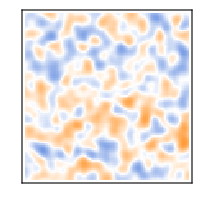
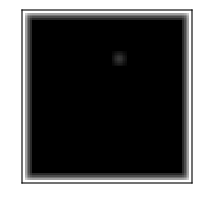
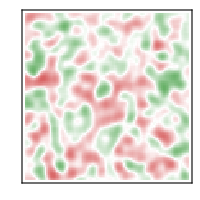
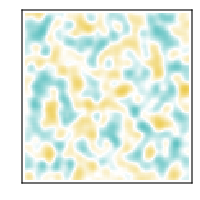
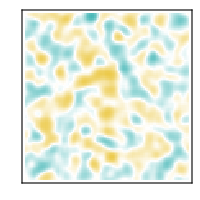
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
latticeGasOrderParameterPlot[configuration,5,ImageSize->200]
```

The composition takes a local average at each lattice site; the values lie between 0 and 1.

The checkerboard phase computes a local order parameter by multiplying each site’s neighborhood with   which will be 9 if the neighborhood is a checkerboard in one registry and -9 in the other.

The two striped phase variant order parameters are obtained with the neighborhood stencils:
  and .

#### higher temperature

and  will favor unlike nearest neighbors and give a checkerboard pattern at τ = 1:

```mathematica
width=height = 30;
configuration =randomConfiguration[1/2,{30,30}];
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^6,
"energyNearest"->1,"energyNextNearest"->0,"inverseTemperature"->1,"exchangeProbability"->0,"occupiedSwitchFrequency"->1,"muBlue"->100,"muOrange"->100
];
```

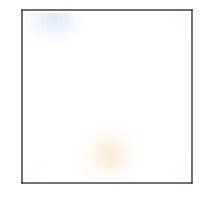
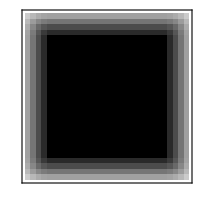
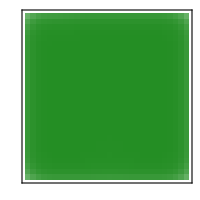
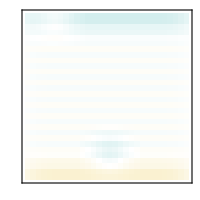
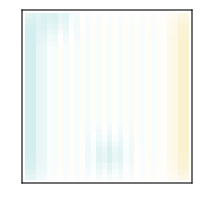
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
latticeGasOrderParameterPlot[configuration,5,ImageSize->200]
```

should produce a checkerboard signal that approaches 1 (there are some edges effects that prevent the value from being exactly 1).  We can measure that by computing the average square order parameter:

```mathematica
orderParameters=latticeGasOrderParameterMaps[configuration,8];

Total[Abs@Flatten@orderParameters["checkerboard"]]/(width height)
```

0.808893

#### higher temperature

But, at higher temperatures τ=3

```mathematica
configuration =randomConfiguration[1/2,{30,30}];
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^7,
"energyNearest"->1,"energyNextNearest"->0,"inverseTemperature"->1/4,"exchangeProbability"->0,"occupiedSwitchFrequency"->1,"muBlue"->100,"muOrange"->100
];
```

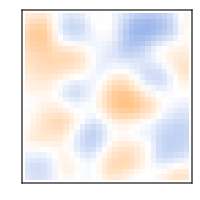
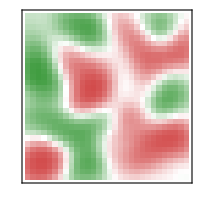
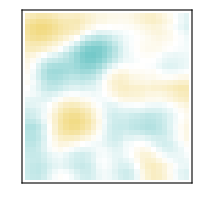
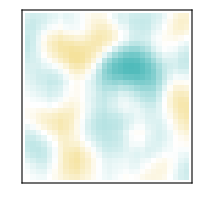
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
latticeGasOrderParameterPlot[configuration,5,ImageSize->200]
```

```mathematica
orderParameters=latticeGasOrderParameterMaps[configuration,8];

Total[Abs@Flatten@orderParameters["checkerboard"]]/(width height)
```

0.12088

The average order parameter should be much less than 1.

To get a sense of how the averaged checkerboard parameter should behave for a typical random configuration:

```mathematica
disorderedParameterSamples =Table[With[{random = randomConfiguration[1/2,{30,30}]},{orderParameters = latticeGasOrderParameterMaps[random,8]},
1/(width height)Total[Abs[Flatten[orderParameters["checkerboard"]]]]
],
1000
];
```

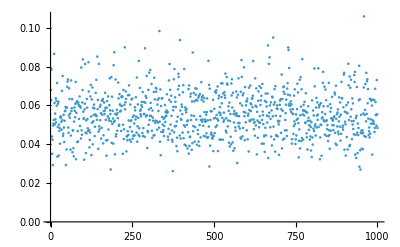

```mathematica
ListPlot[disorderedParameterSamples]
```

```mathematica
Mean[disorderedParameterSamples]
```

0.0553694

### Samples as a function of temperature:

#### Random Starting points

We start with a evenly populated random configuration and anneal it at  a set of temperatures, and then take a thousand samples (each separated by 1000 Metropolis steps).
And then collect the average values

```mathematica
width = height = 100;
Monitor[
orderParameterTemperature =
Table[
configuration =randomConfiguration[1/2,{width,height}];
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^7,
"energyNearest"->1,"energyNextNearest"->0,"muBlue"->100,"muOrange"->100,"inverseTemperature"->1/temperature,"exchangeProbability"->0,"occupiedSwitchFrequency"->1
];
checkerboardSamples=
Table[
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^3,

];
orderParameters=latticeGasOrderParameterMaps[configuration,8];
Total[Abs@Flatten@orderParameters["checkerboard"]],
1000
];
{temperature,Mean[checkerboardSamples]/(width height)}
,
{temperature,3,.1,-.1}
]
,
temperature
]
```

{{3.,0.17536},{2.9,0.192599},{2.8,0.214614},{2.7,0.238869},{2.6,0.263788},{2.5,0.316152},{2.4,0.386138},{2.3,0.495823},{2.2,0.546959},{2.1,0.70746},{2.,0.718349},{1.9,0.790274},{1.8,0.749113},{1.7,0.835564},{1.6,0.823141},{1.5,0.886773},{1.4,0.89132},{1.3,0.86993},{1.2,0.934835},{1.1,0.881734},{1.,0.873955},{0.9,0.850724},{0.8,0.888424},{0.7,0.864795},{0.6,0.910051},{0.5,0.889252},{0.4,0.817614},{0.3,0.834841},{0.2,0.873079},{0.1,0.852168}}

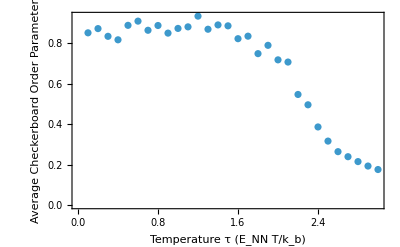

```mathematica
ListPlot[orderParameterTemperature,
Frame->True,FrameLabel->{"Temperature τ (E_NN T/k_b)",
"Average Checkerboard Order Parameter"}
]
```

There is a clear transition between τ- 2 and τ =2.5

Another approach would be to start at  higher temperature and then quenching (i.e., not reinitializing  with a random configuration at each temperature)

```mathematica
width = height = 100;
configuration =randomConfiguration[1/2,{width,height}];
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^7,
"energyNearest"->1,"energyNextNearest"->0,"muBlue"->100,"muOrange"->100,"inverseTemperature"->1/3.0,"exchangeProbability"->0,"occupiedSwitchFrequency"->1
];


Monitor[
orderParameterTemperatureQuench =
Table[
checkerboardSamples=
Table[
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^4,

];
orderParameters=latticeGasOrderParameterMaps[configuration,8];
Total[Abs@Flatten@orderParameters["checkerboard"]],
1000
];
{temperature,Mean[checkerboardSamples]/(width height)}
,
{temperature,3,.1,-.1}
]
,
temperature
]
```

{{3.,0.181036},{2.9,0.1963},{2.8,0.212018},{2.7,0.232352},{2.6,0.274389},{2.5,0.311353},{2.4,0.370036},{2.3,0.472939},{2.2,0.605426},{2.1,0.748802},{2.,0.834689},{1.9,0.875495},{1.8,0.898123},{1.7,0.909158},{1.6,0.919956},{1.5,0.926452},{1.4,0.932312},{1.3,0.936563},{1.2,0.938339},{1.1,0.940654},{1.,0.940843},{0.9,0.941366},{0.8,0.941594},{0.7,0.941765},{0.6,0.941818},{0.5,0.941767},{0.4,0.941887},{0.3,0.941904},{0.2,0.941905},{0.1,0.941905}}

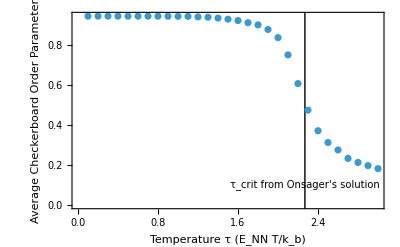

```mathematica
ListPlot[orderParameterTemperatureQuench,
Frame->True,FrameLabel->{"Temperature τ (E_NN T/k_b)",
"Average Checkerboard Order Parameter"},
Epilog->{
InfiniteLine[{τCrit,0},{0,1}],
Text[Style["τ_crit from Onsager's solution",10],{τCrit,0.1},{1.1,0}]
}
]
```

The simulation picks up the exact solution.  This has the characteristics of a second-order phase transition (the order parameter changes continuously across the critical temperature). However, in a finite system, even a first order transition would have this continuous behavior—so, our result is not necessarily evidence that the order-disorder transition is first or second order.

## Transitions with second nearest neighbor interactions.

Let’s turn on a second neighbor interaction.  If  it will tend to disfavor like second nearest neighbors, so it should not favor a checkerboard phase.  Let’s see how a value of   affects the critical transition temperature:

```mathematica
width = height = 100;
enn = 1.0; ennn=1/4

configuration =randomConfiguration[1/2,{width,height}];
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^7,
"energyNearest"->enn,"energyNextNearest"->ennn,"muBlue"->100,"muOrange"->100,"inverseTemperature"->1/3.0,"exchangeProbability"->0,"occupiedSwitchFrequency"->1
];


Monitor[
orderParameterTemperatureQuenchWithSNN =
Table[
checkerboardSamples=
Table[
{configuration, statistics} =latticeGasMetropolisSweep[configuration,10^4,
"energyNearest"->enn,"energyNextNearest"->ennn,"muBlue"->100,"muOrange"->100,"inverseTemperature"->1/temperature,"exchangeProbability"->0,"occupiedSwitchFrequency"->1
];
orderParameters=latticeGasOrderParameterMaps[configuration,8];
Total[Abs@Flatten@orderParameters["checkerboard"]],
1000
];
{temperature,Mean[checkerboardSamples]/(width height)}
,
{temperature,3,.1,-.1}
]
,
temperature
]
```

1/4

{{3.,0.105418},{2.9,0.108621},{2.8,0.111755},{2.7,0.115329},{2.6,0.120195},{2.5,0.124733},{2.4,0.130053},{2.3,0.136814},{2.2,0.144714},{2.1,0.158592},{2.,0.170087},{1.9,0.184744},{1.8,0.212472},{1.7,0.24786},{1.6,0.321373},{1.5,0.415799},{1.4,0.578869},{1.3,0.766922},{1.2,0.83596},{1.1,0.858059},{1.,0.866715},{0.9,0.876745},{0.8,0.881113},{0.7,0.883501},{0.6,0.883562},{0.5,0.884651},{0.4,0.885106},{0.3,0.885233},{0.2,0.885174},{0.1,0.885249}}

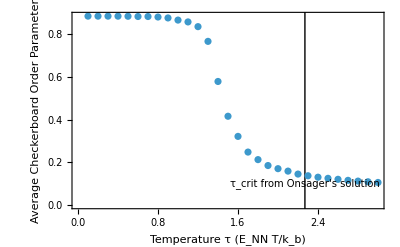

```mathematica
ListPlot[orderParameterTemperatureQuenchWithSNN,
Frame->True,FrameLabel->{"Temperature τ (E_NN T/k_b)",
"Average Checkerboard Order Parameter"},
Epilog->{
InfiniteLine[{τCrit,0},{0,1}],
Text[Style["τ_crit from Onsager's solution",10],{τCrit,0.1},{1.1,0}]
}
]
```

This is consistent with our physical intuition.  The destabilizing term causes the sytem to disorder at lower temperatures.